# Time Constant Calculator from Simulation Data

## Setup (automatically initialized when this notebook is opened)

### Function definitions

#### OrganizeWFData[fileName_,timeBounds_]

This function takes the filename of a waveform and extracts the coordinates of the waveform plot.  It also takes the timeBounds variable as input.  timeBounds is a variable that defines the start and stop times between which the data should be taken.

As output, this function returns a single data member which is organized as {}.

```mathematica
OrganizeWFData[fileName_]:=Module[{axesLabel,d,i},
i=Import[fileName,"Data"];
axesLabel=i⟦1⟧;
d=i⟦2;;⟧;
Return[{axesLabel,d}];
](* OrganizeWFData Module *)
```

### Ask user to select an input file with the waveform data

This section opens a system dialog box that asks the user to select a waveform file with the waveform trace.  It then sets the default working directory equal to the directory where this file is located.

```mathematica
fileName=SystemDialogInput["FileOpen","/home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements", WindowTitle->"Select Simulation Waveform File (*.txt)"];
workingDir=DirectoryName[fileName];
SetDirectory[workingDir];
Print[Style["Working Directory:  ",FontFamily->"Helvetica", Bold] ,Style[Directory[],Italic]]
Print[Style["File Name: ", FontFamily->"Helvetica", Bold],FileNameTake[fileName]];
```

Working Directory:  /home/noza/work/Mathematica/Scripts/LPFTimeConstantMeasurements

File Name: LPFWaveform_Im_tau_0.010_Immax214f.txt

## Information Processing (Run-time) - Rising Edge

### Process Waveform Data from Input File

This section takes the fileName gotten from the selection dialog and imports the data using the OrganizeWFData function defined in the functions section.  It then filters that data to the selected region, where the selected region specifies the data points that fit an exponential decay model.

```mathematica
timeBoundsRE ={0.1,0.4};
AbsoluteTiming[{axesLabelRE,dataRE}=OrganizeWFData[fileName]];(*Import data*)
(* Filter out data to get just the decay portion of the curve *)
offsetMinsRE=dataRE⟦1,2⟧-10^-17;
timeFilteredDataRE=Select[dataRE,#⟦1⟧>timeBoundsRE⟦1⟧&];
timeFilteredDataRE=Select[timeFilteredDataRE,#⟦1⟧<=timeBoundsRE⟦2⟧&];
(*timeFilteredDataRE=DataToPlotFormat[timeFilteredDataRE];(*Organize data to allow it to be plottable*)*)
(*dRE=DataToPlotFormat[dataRE];(*Organize data to allow it to be plottable*)*)
(* Extract tau values and labels from imported dataset *)
(*tauLabelsRE=Rest[axesLabelRE];
tauValsRE=ToExpression[Flatten[StringCases[tauLabelsRE,"i(vmeas_im):tau_"~~tauRE:NumberString~~"`"-> tauRE]]];*)
IsatsRE=Max[timeFilteredDataRE⟦;;,2⟧];
(*offsetMinsRE=Min[timeFilteredDataRE⟦;;,2⟧]-10^-17*)
(* Take only positive current values after subtracting Offset away as valid data *)
offsetLessDataRE=timeFilteredDataRE-offsetMinsRE;
validTimeFilteredDataRE=Select[offsetLessDataRE,#⟦2⟧>0&];
(*Get important values for fitting a linear fit*)

(* Clear timeFilteredData from memory *)
Clear[timeFilteredDataRE];
```

### Plot Data

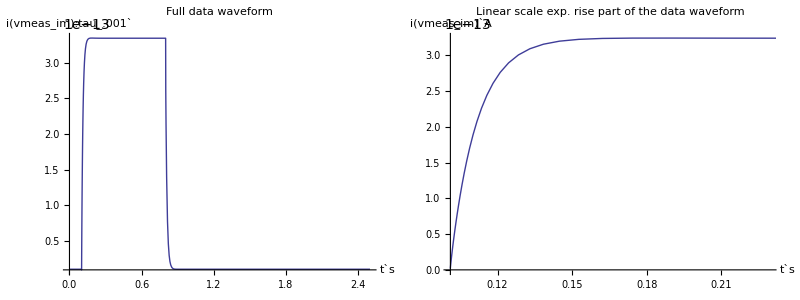
Data Waveforms
-Graphics-

```mathematica
imgSizeRE=350;
Grid[{
{Text[Style["Data Waveforms",Bold,18]]},
{Grid[{
{ListLinePlot[dataRE,AxesLabel->axesLabel,ImageSize->imgSizeRE, PlotLabel->Style["Full data waveform",Bold],PlotRange->{Automatic,All}],
ListLinePlot[validTimeFilteredDataRE,AxesLabel->axesLabelRE,ImageSize->imgSizeRE, PlotLabel->Style["Linear scale exp. rise part of the data waveform",Bold]](*,
ListLogPlot[validTimeFilteredDataRE,AxesLabel->axesLabelRE,Joined->True,ImageSize->imgSizeRE, PlotLabel->Style["Log scale exp. rise part of the data waveform",Bold]]*)
}}]}
}]
```

### Manipulate Data

#### Calculate τ using linear fit manually accounting for offset

```mathematica
imgSizeRE=400;
workPrecRE=Automatic;
tauValRE=.010
(* Extract x-values from dataset *)
xValsRE=Transpose[validTimeFilteredDataRE]⟦1⟧;
TabView[{
"Linear Log Fit"->
Manipulate[
(*plotNumRE=Sequence@@Flatten[Position[tauValsRE,plotIDRE]];*)

xValsRE=Transpose[validTimeFilteredDataRE]⟦1⟧;
(* Select exponential range of data *)
boundedOffsetLessDataRE=Select[validTimeFilteredDataRE,#⟦1⟧>=lowerBoundRE&];
boundedOffsetLessDataRE=Select[boundedOffsetLessDataRE,#⟦1⟧<=upperBoundRE&];
(* Shift the data so that the exponential curve is shifted left, such that the curve crosses the y-axis at the correct Isat value *)
shiftedBoundedOffsetLessDataRE=Transpose[{boundedOffsetLessDataRE⟦;;,1⟧-lowerBoundRE,boundedOffsetLessDataRE⟦;;,2⟧}];
logOffsetLessDataRE=Transpose[{shiftedBoundedOffsetLessDataRE⟦;;,1⟧,Log[(IsatsRE-shiftedBoundedOffsetLessDataRE⟦;;,2⟧)/(IsatsRE-offsetMinsRE)]}];

(* Find the best fit *)
fitLineEqRE=Fit[logOffsetLessDataRE,{1,t},t];
fitLineRulesRE=FindFit[logOffsetLessDataRE,m t+b,{{m,-1/tauValRE},b},t];
τRE=-1/m/.fitLineRulesRE;
errTauRE=Abs[τRE-tauValRE];percErrTauRE=(errTauRE/tauValRE)*100;
(*A little memory management*)
Clear[boundedOffsetLessDataRE, offsetLessDataRE];
Grid[{
{(*Row[{Style["ι_in:  ",FontFamily->"Helvetica", Bold] ,Style[iInVal,Italic]}],*)
Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}]},
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[IsatsRE,Italic]}](*,
Row[{Style["Extracted Isat:  ",FontFamily->"Helvetica", Bold] ,Style[ⅇ^b/.fitLineRulesRE,Italic]}]*)},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[offsetMinsRE,Italic]}]},
{Show[(*ListPlot[logSelData,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],*)
ListPlot[logOffsetLessDataRE,AxesLabel->axesLabelRE,ImageSize->imgSizeRE,PlotRange->{{0,upperBoundRE-lowerBoundRE},{All,0}},PlotStyle->Red],
Plot[fitLineEqRE,{t,0,upperBoundRE-lowerBoundRE}]
]},
{Grid[{
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τRE,Italic]}]},
{Row[{Style["Δτ:  ",FontFamily->"Helvetica", Bold] ,Style[errTauRE,Italic]}]},
{Row[{Style["τ_err(%):  ",FontFamily->"Helvetica", Bold] ,Style[percErrTauRE,Italic]}]}
}]}
}],
(*{{plotIDRE,tauValsRE⟦defaultPlotNumRE⟧,"Theoretical τ Value"},tauValsRE},*)
{{lowerBoundRE,xValsRE⟦1⟧,"Lower Bound"},Dynamic[Take[xValsRE,Ceiling[Length[xValsRE]*3/4]]],Appearance->{"Labeled","Open"}},
{{upperBoundRE,xValsRE⟦Floor[Length[Most[xValsRE]]]⟧,"Upper Bound"},Dynamic[Most[xValsRE]],Appearance->{"Labeled","Open"}},
LabelStyle->Medium,
UnsavedVariables->{fitLineEqRE,fitLineRulesRE,errTauRE,logOffsetLessDataRE,shiftedBoundedOffsetLessDataRE,τRE,xValsRE},
TrackedSymbols->{lowerBoundRE,upperBoundRE}
](*Manipulate Linear *)
},1](*TabView *)
```

0.01

1

Thread::tdlen: Objects of unequal length in TraditionalForm`{{0.100001, 1.03026×10^-14}, {0.100004, 1.03022×10^-14}, {0.100013, 1.03009×10^-14}, {0.10004, 1.02969×10^-14}, {0.100128, 1.0285×10^-14}, {0.100409, 1.02543×10^-14}, {0.101071, 1.02243×10^-14}, {0.101787, 1.02527×10^-14}, {0.102628, 1.03611×10^-14}, « 33 », {0.150388, 1.46357×10^-13}, {0.154326, 1.49913×10^-13}, {0.158656, 1.5335×10^-13}, {0.163099, 1.56282×10^-13}, {0.168971, 1.593×10^-13}, {0.177525, 1.62468×10^-13}, {0.185705, 1.64573×10^-13}, {0.198284, 1.66701×10^-13}, « 5 »} + {« 1 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

$Aborted

Plot::plln: Limiting value TraditionalForm`{{0.100001, 1.03026×10^-14}, {0.100004, 1.03022×10^-14}, {0.100013, 1.03009×10^-14}, {0.10004, 1.02969×10^-14}, {0.100128, 1.0285×10^-14}, {0.100409, 1.02543×10^-14}, {0.101071, 1.02243×10^-14}, {0.101787, 1.02527×10^-14}, {0.102628, 1.03611×10^-14}, « 33 », {0.150388, 1.46357×10^-13}, {0.154326, 1.49913×10^-13}, {0.158656, 1.5335×10^-13}, {0.163099, 1.56282×10^-13}, {0.168971, 1.593×10^-13}, {0.177525, 1.62468×10^-13}, {0.185705, 1.64573×10^-13}, {0.198284, 1.66701×10^-13}, « 5 »} + {« 1 »} in TraditionalForm`{t, 0, FE`upperBoundRE$$284 - FE`lowerBoundRE$$284} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

Select::normal: Nonatomic expression expected at position TraditionalForm`1 in TraditionalForm`Select[validTimeFilteredDataRE, #1 ⟦ 1 ⟧ ≥ FE`lowerBoundRE$$313 &].

Part::partd: Part specification TraditionalForm`validTimeFilteredDataRE ⟦ 1 ⟧ is longer than depth of object.

Select::argt: TraditionalForm`Select called with TraditionalForm`0 arguments; TraditionalForm`2 or TraditionalForm`3 arguments are expected.

General::stop: Further output of Select :: argt will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list TraditionalForm`{{{-0.100001 + Select[], -1.10956×10^-14 + Select[]}, {-0.100004 + Select[], -1.10133×10^-14 + Select[]}, {-0.100013 + Select[], -1.07582×10^-14 + Select[]}, {-0.10004 + Select[], -1.002×10^-14 + Select[]}, {-0.100073 + Select[], -9.26415×10^-15 + Select[]}, « 42 », {-0.102046 + Select[], -2.41735×10^-12 + Select[]}, {-0.102138 + Select[], -2.50712×10^-12 + Select[]}, {-0.102248 + Select[], -2.59372×10^-12 + Select[]}, « 25 »}, Select[]} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list TraditionalForm` cannot be transposed.

Fit::fitd: First argument … in Fit is not a list or a rectangular array.

FindFit::srect: Value TraditionalForm`-1/tauValRE in search specification TraditionalForm`{m, -1/tauValRE} is not a number or array of numbers.

General::stop: Further output of FindFit :: srect will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in TraditionalForm`{{0.100001, 1.03026×10^-14}, {0.100004, 1.03022×10^-14}, {0.100013, 1.03009×10^-14}, {0.10004, 1.02969×10^-14}, {0.100128, 1.0285×10^-14}, {0.100409, 1.02543×10^-14}, {0.101071, 1.02243×10^-14}, {0.101787, 1.02527×10^-14}, « 35 », {0.154326, 1.49913×10^-13}, {0.158656, 1.5335×10^-13}, {0.163099, 1.56282×10^-13}, {0.168971, 1.593×10^-13}, {0.177525, 1.62468×10^-13}, {0.185705, 1.64573×10^-13}, {0.198284, 1.66701×10^-13}, « 5 »} + {{« 1 »}, « 49 », « 25 »} cannot be combined.

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

Thread::tdlen: Objects of unequal length in TraditionalForm`{{0.100001, 1.03026×10^-14}, {0.100004, 1.03022×10^-14}, {0.100013, 1.03009×10^-14}, {0.10004, 1.02969×10^-14}, {0.100128, 1.0285×10^-14}, {0.100409, 1.02543×10^-14}, {0.101071, 1.02243×10^-14}, {0.101787, 1.02527×10^-14}, « 35 », {0.154326, 1.49913×10^-13}, {0.158656, 1.5335×10^-13}, {0.163099, 1.56282×10^-13}, {0.168971, 1.593×10^-13}, {0.177525, 1.62468×10^-13}, {0.185705, 1.64573×10^-13}, {0.198284, 1.66701×10^-13}, « 5 »} + {{« 1 »}, « 49 », « 25 »} cannot be combined.

Plot::plln: Limiting value TraditionalForm`{{0.100001, 1.03026×10^-14}, {0.100004, 1.03022×10^-14}, {0.100013, 1.03009×10^-14}, {0.10004, 1.02969×10^-14}, {0.100128, 1.0285×10^-14}, {0.100409, 1.02543×10^-14}, {0.101071, 1.02243×10^-14}, {0.101787, 1.02527×10^-14}, « 35 », {0.154326, 1.49913×10^-13}, {0.158656, 1.5335×10^-13}, {0.163099, 1.56282×10^-13}, {0.168971, 1.593×10^-13}, {0.177525, 1.62468×10^-13}, {0.185705, 1.64573×10^-13}, {0.198284, 1.66701×10^-13}, « 5 »} + {{« 1 »}, « 49 », « 25 »} in TraditionalForm`{t, 0, FE`upperBoundRE$$313 - FE`lowerBoundRE$$313} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

Select::normal: Nonatomic expression expected at position TraditionalForm`1 in TraditionalForm`Select[validTimeFilteredDataRE, #1 ⟦ 1 ⟧ ≥ FE`lowerBoundRE$$313 &].

Part::partd: Part specification TraditionalForm`validTimeFilteredDataRE ⟦ 1 ⟧ is longer than depth of object.

Select::argt: TraditionalForm`Select called with TraditionalForm`0 arguments; TraditionalForm`2 or TraditionalForm`3 arguments are expected.

$Aborted

General::stop: Further output of Select :: argt will be suppressed during this calculation.

Transpose::nmtx: The first two levels of the one-dimensional list TraditionalForm`{{{-0.100001 + Select[], -1.10956×10^-14 + Select[]}, {-0.100004 + Select[], -1.10133×10^-14 + Select[]}, {-0.100013 + Select[], -1.07582×10^-14 + Select[]}, {-0.10004 + Select[], -1.002×10^-14 + Select[]}, {-0.100073 + Select[], -9.26415×10^-15 + Select[]}, « 42 », {-0.102046 + Select[], -2.41735×10^-12 + Select[]}, {-0.102138 + Select[], -2.50712×10^-12 + Select[]}, {-0.102248 + Select[], -2.59372×10^-12 + Select[]}, « 25 »}, Select[]} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list TraditionalForm` cannot be transposed.

$Aborted

FindFit::srect: Value TraditionalForm`-1/tauValRE in search specification TraditionalForm`{m, -1/tauValRE} is not a number or array of numbers.

General::stop: Further output of FindFit :: srect will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in TraditionalForm`{{0.100001, 1.03026×10^-14}, {0.100004, 1.03022×10^-14}, {0.100013, 1.03009×10^-14}, {0.10004, 1.02969×10^-14}, {0.100128, 1.0285×10^-14}, {0.100409, 1.02543×10^-14}, {0.101071, 1.02243×10^-14}, {0.101787, 1.02527×10^-14}, « 35 », {0.154326, 1.49913×10^-13}, {0.158656, 1.5335×10^-13}, {0.163099, 1.56282×10^-13}, {0.168971, 1.593×10^-13}, {0.177525, 1.62468×10^-13}, {0.185705, 1.64573×10^-13}, {0.198284, 1.66701×10^-13}, « 5 »} + {{« 1 »}, « 49 », « 25 »} cannot be combined.

## Appendix

#### Calculate τ using exponential fit including offset

```mathematica
Manipulate[
dataBoundsExp={lowerBoundExp,upperBoundExp};
selectedDataExp=Select[selectedData,#⟦2⟧>0&];
xValsExp=Transpose[selectedDataExp]⟦1⟧;
selDataExp=Select[selectedDataExp,#⟦1⟧>dataBoundsExp⟦1⟧&];
selDataExp=Select[selDataExp,#⟦1⟧<dataBoundsExp⟦2⟧&];
(*fooLine=Fit[selDataExp,{1,Exp[-t]},t]*)
model=(a Exp[-t/τexp])+o;
fooCurveParams=FindFit[selDataExp,model,{a,τexp,o},t,MaxIterations->10000];
fooCurve=Function[{t},Evaluate[model/.fooCurveParams]];
Grid[{
{Row[{Style["File Name:  ",FontFamily->"Helvetica", Bold] ,Style[FileNameTake[fileName],Italic]}]},
{Row[{Style["Measured Isat:  ",FontFamily->"Helvetica", Bold] ,Style[a/.fooCurveParams,Italic]}]},
{Row[{Style["Measured offset:  ",FontFamily->"Helvetica", Bold] ,Style[o/.fooCurveParams,Italic]}]},
{Row[{Style["Calculated τ:  ",FontFamily->"Helvetica", Bold] ,Style[τexp/.fooCurveParams,Italic]}]},
{Show[ListPlot[selDataExp,AxesLabel->axesLabel,ImageSize->imgSize,PlotStyle->Red],
ListLogPlot[selDataExp,AxesLabel->axesLabel,ImageSize->imgSize],
Plot[fooCurve[t],{t,0,upperBoundExp}]
]}
}],
{{lowerBoundExp,0.501,"Lower Bound"},0.5,1.0,.001,Appearance->{"Labeled","Open"}},
{{upperBoundExp,xValsExp⟦Floor[Length[Most[xValsExp]]]⟧,"Upper Bound"},Most[xValsExp],Appearance->{"Labeled","Open"}}
]
```

### Data Analysis (taken from Multiple input version, but hasn’t been adapted to this notebook)

#### Accuracy of Tau Values as measured from the exponential fit manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawDataExp=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.2781, .2892, .2856, .288, .2593, .198, .1511}, {0.5, .0055, .0036, .0162, .0023, .0021, .0022, .0012}, {0.75, .0005, .0037, .0002, .0002, .00003, .0026, .0044}, {1.00, .0007, .0001, .0021, .00003, .0017, .0032, .0031}, {1.25, .0021, .0008, .0006, .0002, .0012, .0002, .0012}, {3, .0001, .0020, .0008, .00005, .0004, .0011, .0004}});
percErrTauValsExp=Rest[percErrTauRawDataExp⟦1⟧];
percErriinValsExp=Rest[Transpose[percErrTauRawDataExp]⟦1⟧];
percErrPlotValsExp=Transpose[Rest[Transpose[Rest[percErrTauRawDataExp]]]];
MatrixPlot[percErrPlotValsExp,PlotRange->{Min[percErrPlotValsExp],Max[percErrPlotValsExp]},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

-Graphics-

#### Accuracy of Tau Values as measured from the linear fit manipulator

This table will hold the data obtained manually from playing with the manipulator to find the minimum percentage error in tau.

```mathematica
percErrTauRawData=({{0, .001, .002, .005, .010, .015, .020, .025}, {0.25, 0.4270, 0.4105, 0.3824, 0.3208, 0.2499, 0.1815, 0.1276}, {0.5, 0.0672, 0.0546, 0.0473, 0.0336, 0.0172, 0.0105, 0.0005}, {0.75, 0.0049, 0.0013, 0.0002, 0.0018, 0.0013, 0.0007, 0.0006}, {1.00, 0.0014, 0.0011, 0.0025, 0.0015, 0.0023, 0.0019, 0.0008}, {1.25, 0.0004, 0.0039, 0.0010, 0.0022, 0.0018, 0.0027, 0.0003}, {3, 0.0039, 0.0047, 0.0018, 0.0025, 0.0036, 0.0026, 0.0025}});
percErrTauVals=Rest[percErrTauRawData⟦1⟧];
percErriinVals=Rest[Transpose[percErrTauRawData]⟦1⟧];
percErrPlotVals=Transpose[Rest[Transpose[Rest[percErrTauRawData]]]];
MatrixPlot[percErrPlotVals,PlotRange->{Min[percErrPlotVals],Max[percErrPlotVals]},ColorFunctionScaling->True,ColorFunction->"CherryTones",PlotLabel->"Percentage Error of τ",AxesLabel->{"Expected τ value","ι_in value"},PlotLegends->True]
```

-Graphics-